```mathematica
Range[1,5]
```

{1,2,3,4,5}

```mathematica
diffDataSmall=Import["/Users/benxgh1996/Desktop/wave_particle_duality/results.xlsx",{"Data",1,Range[3,17],{1,2}}]
```

{{0.0258199,0.0786846},{0.0239046,0.0732111},{0.0223607,0.067734},{0.0210819,0.0640808},{0.02,0.0595124},{0.0190693,0.0576845},{0.0182574,0.0558563},{0.0175412,0.0540278},{0.0169031,0.052199},{0.0163299,0.0503699},{0.0158114,0.0485405},{0.0153393,0.0476258},{0.0149071,0.0439661},{0.0145095,0.0439661},{0.0141421,0.043051}}

```mathematica
Length[diffDataSmall]
```

15

```mathematica
diffDataLarge=Import["/Users/benxgh1996/Desktop/wave_particle_duality/results.xlsx",{"Data",1,Range[3,17],{1,3}}]
```

{{0.0258199,0.13317},{0.0239046,0.125936},{0.0223607,0.119598},{0.0210819,0.111438},{0.02,0.105991},{0.0190693,0.0996296},{0.0182574,0.0941719},{0.0175412,0.0914413},{0.0169031,0.0914413},{0.0163299,0.0877988},{0.0158114,0.0868879},{0.0153393,0.0814201},{0.0149071,0.0786846},{0.0145095,0.0768605},{0.0141421,0.0741236}}

```mathematica
Length[diffDataLarge]
```

15

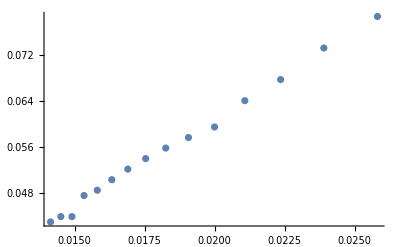

```mathematica
ListPlot[diffDataSmall]
```

```mathematica
FindFit[diffDataSmall,a x,a,x]
```

{a→3.04511}

```mathematica
k/3.045109346457716
```

2.01376×10^-10

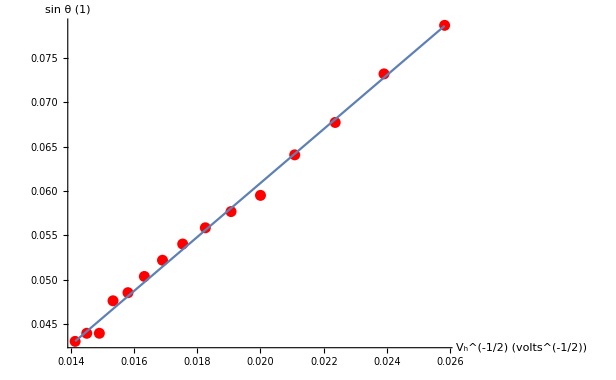

```mathematica
Show[ListPlot[diffDataSmall,PlotStyle->Red],Plot[a x/.{a->3.045109346457716},{x,0.01414213562373095,0.02581988897471611}],AxesLabel-> {"   V_h^(-1/2) (volts^(-1/2))","sin θ (1)"},BaseStyle->{FontSize->16}]
```

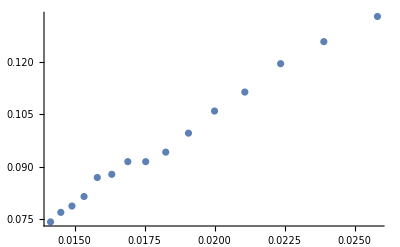

```mathematica
ListPlot[diffDataLarge]
```

```mathematica
FindFit[diffDataLarge, b x, b,x]
```

{b→5.27882}

```mathematica
k/5.278824035600507
```

1.16165×10^-10

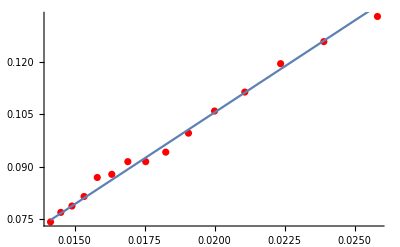

```mathematica
Show[ListPlot[diffDataLarge,PlotStyle->Red],Plot[b x/.{b->5.278824035600507},{x,0.01414213562373095,0.02581988897471611}],AxesLabel-> {"   V_h^(-1/2) (volts^(-1/2))","sin θ (1)"},BaseStyle->{FontSize->16}]
```

```mathematica
m=9.10938215*10^-31
```

9.10938×10^-31

```mathematica
e=1.602176487*10^-19
```

1.60218×10^-19

```mathematica
h=6.62606896*10^-34
```

6.62607×10^-34

```mathematica
k=h/(√(8 m e))
```

6.13213×10^-10

```mathematica
diffDataSmallInner=Import["/Users/benxgh1996/Desktop/wave_particle_duality/results.xlsx",{"Data",1,Range[3,17],{1,4}}]
```

{{0.0258199,0.06956},{0.0239046,0.067734},{0.0223607,0.0604262},{0.0210819,0.0585985},{0.02,0.0531134},{0.0190693,0.0531134},{0.0182574,0.0512845},{0.0175412,0.0494552},{0.0169031,0.0476258},{0.0163299,0.0457961},{0.0158114,0.0439661},{0.0153393,0.0439661},{0.0149071,0.0403055},{0.0145095,0.0403055},{0.0141421,0.0384749}}

```mathematica
Length[diffDataSmallInner]
```

15

```mathematica
diffDataLargeInner=Import["/Users/benxgh1996/Desktop/wave_particle_duality/results.xlsx",{"Data",1,Range[3,17],{1,5}}]
```

{{0.0258199,0.125936},{0.0239046,0.11688},{0.0223607,0.111438},{0.0210819,0.104174},{0.02,0.100539},{0.0190693,0.0950818},{0.0182574,0.0877988},{0.0175412,0.0859769},{0.0169031,0.0859769},{0.0163299,0.0823316},{0.0158114,0.0805084},{0.0153393,0.0768605},{0.0149071,0.0732111},{0.0145095,0.0732111},{0.0141421,0.06956}}

```mathematica
Length[%]
```

15

```mathematica
FindFit[diffDataSmallInner,a x,a,x]
```

{a→2.76415}

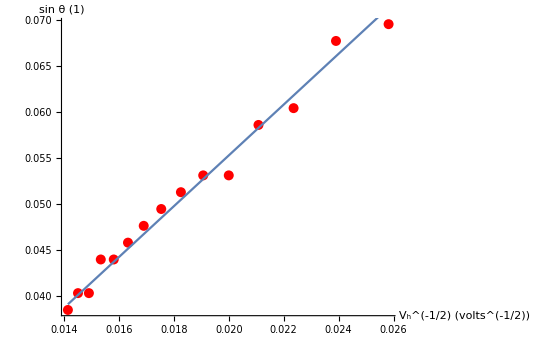

```mathematica
Show[ListPlot[diffDataSmallInner,PlotStyle->Red],Plot[a x/.{a->2.7641487831096034},{x,0.01414213562373095,0.02581988897471611}],AxesLabel-> {"   V_h^(-1/2) (volts^(-1/2))","sin θ (1)"},BaseStyle->{FontSize->16}]
```

```mathematica
FindFit[diffDataLargeInner,a x,a,x]
```

{a→4.95579}

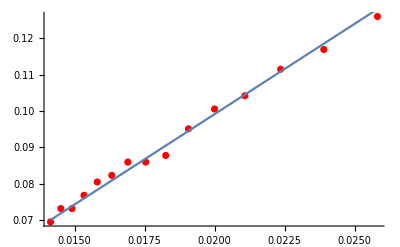

```mathematica
Show[ListPlot[diffDataLargeInner,PlotStyle->Red],Plot[a x/.{a->4.9557920617497935},{x,0.01414213562373095,0.02581988897471611}]]
```

```mathematica
diffDataSmallOuter=Import["/Users/benxgh1996/Desktop/wave_particle_duality/results.xlsx",{"Data",1,Range[3,17],{1,6}}]
```

{{0.0258199,0.0877988},{0.0239046,0.0786846},{0.0223607,0.075036},{0.0210819,0.06956},{0.02,0.0659075},{0.0190693,0.0622537},{0.0182574,0.0604262},{0.0175412,0.0585985},{0.0169031,0.0567704},{0.0163299,0.054942},{0.0158114,0.0531134},{0.0153393,0.0512845},{0.0149071,0.0476258},{0.0145095,0.0476258},{0.0141421,0.0476258}}

```mathematica
Length[%]
```

15

```mathematica
FindFit[diffDataSmallOuter,a x,a,x]
```

{a→3.32591}

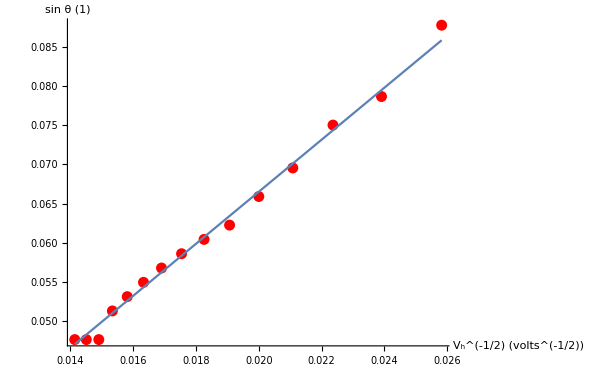

```mathematica
Show[ListPlot[diffDataSmallOuter,PlotStyle->Red],Plot[a x/.{a->3.3259050627398317},{x,0.01414213562373095,0.02581988897471611}],AxesLabel-> {"   V_h^(-1/2) (volts^(-1/2))","sin θ (1)"},BaseStyle->{FontSize->16}]
```

```mathematica
diffDataLargeOuter=Import["/Users/benxgh1996/Desktop/wave_particle_duality/results.xlsx",{"Data",1,Range[3,17],{1,7}}]
```

{{0.0258199,0.140391},{0.0239046,0.134976},{0.0223607,0.127746},{0.0210819,0.118692},{0.02,0.111438},{0.0190693,0.104174},{0.0182574,0.100539},{0.0175412,0.0969014},{0.0169031,0.0969014},{0.0163299,0.0932618},{0.0158114,0.0932618},{0.0153393,0.0859769},{0.0149071,0.0841545},{0.0145095,0.0805084},{0.0141421,0.0786846}}

```mathematica
Length[%]
```

15

```mathematica
FindFit[diffDataLargeOuter,a x,a,x]
```

{a→5.60149}

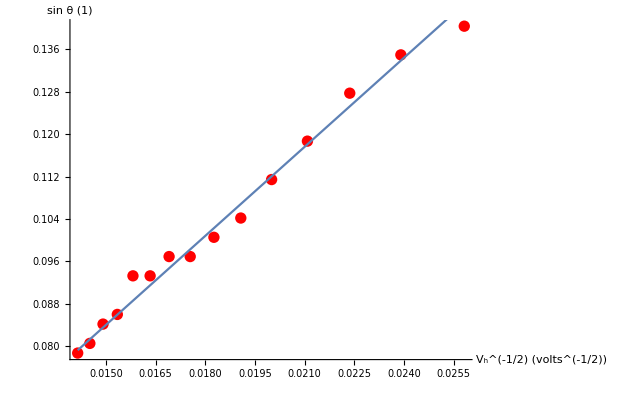

```mathematica
Show[ListPlot[diffDataLargeOuter,PlotStyle->Red],Plot[a x/.{a->5.601487266764604},{x,0.01414213562373095,0.02581988897471611}],AxesLabel-> {"   V_h^(-1/2) (volts^(-1/2))","sin θ (1)"},BaseStyle->{FontSize->16}]
```